```mathematica
SetDirectory["C:\\Python32\\HeatBumpGUI\\mathematica_output"]
```

C:\Python32\HeatBumpGUI\mathematica_output

```mathematica
power=Import["power.dat"];
```

```mathematica
ListPlot3D[power]
```

-Graphics3D-

```mathematica
density=Import["power_density.dat"]
```

```mathematica
ListPlot3D[density2]
```

-Graphics3D-

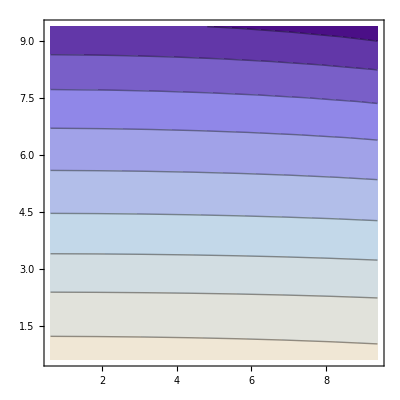

```mathematica
ListContourPlot[density2]
```

```mathematica
density2=f/@density;
```

```mathematica
Log[10,10]//N
```

1.

```mathematica
a={Import["source_flux_0.dat"],Import["source_flux_333.dat"],Import["source_flux_666.dat"],Import["source_flux_999.dat"],Import["source_flux_1999.dat"],Import["source_flux_1999.dat"],Import["source_flux_3999.dat"],Import["source_flux_4999.dat"]};
```

```mathematica
f={#[[1]],#[[2]],Log[10,#[[3]]]}&
```

{#1⟦1⟧,#1⟦2⟧,Log[10,#1⟦3⟧]}&

```mathematica
a2=Table[f/@a[[i]],{i,1,8}];
```

```mathematica
Table[ListPlot3D[a[[i]],PlotRange->{{0,17.5},{0,4},{0,4*^14}}],{i,1,8}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Table[ListPlot3D[a[[i]],PlotRange->All],{i,1,8}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

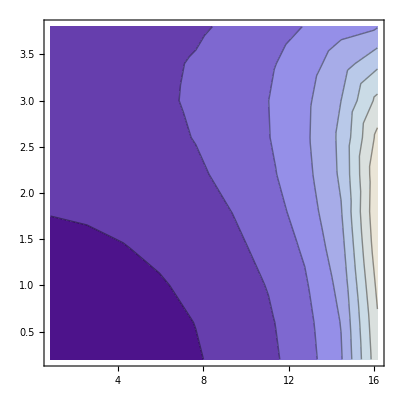
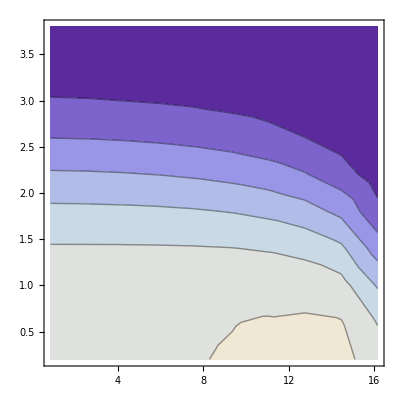
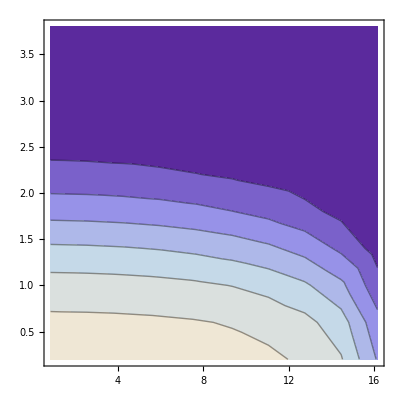
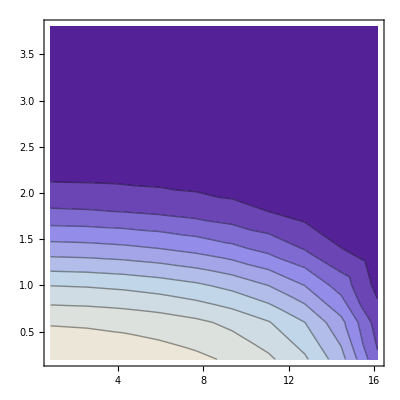
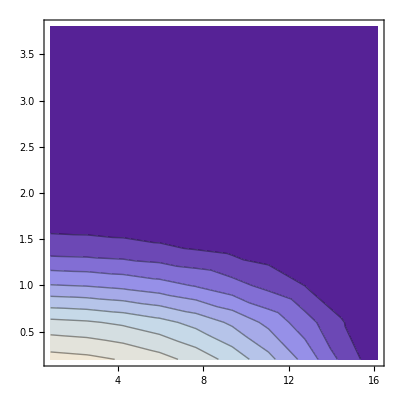
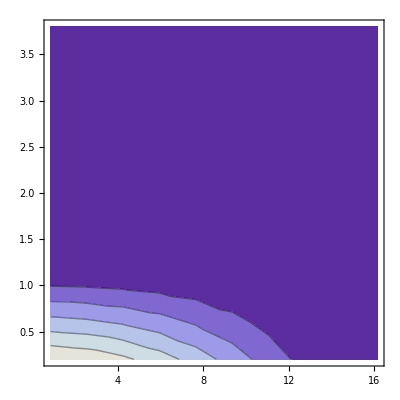
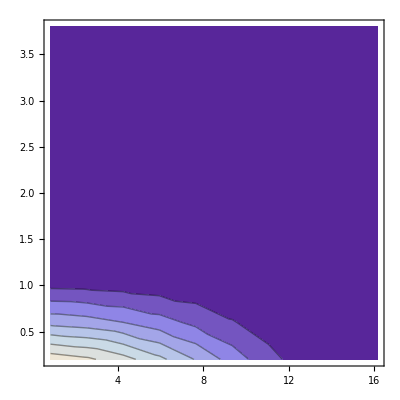
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListContourPlot[a[[i]],PlotRange->All],{i,1,8}]
```

```mathematica
ListPlot3D[a,PlotRange->All]
```

-Graphics3D-

```mathematica
Directory[]
```

C:\Python32\HeatBumpGUI\mathematica_output

```mathematica
power2=Import["power.dat"];
ListPlot3D[power2]
```

-Graphics3D-

```mathematica
d=Import["power_density.dat"];
d2=f/@d;
```

-Graphics3D-

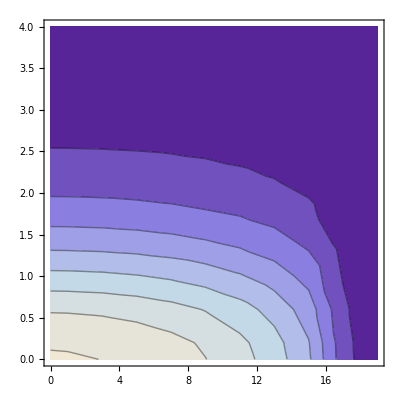

```mathematica
ListPlot3D[d,PlotRange->All]
ListContourPlot[d,PlotRange->All]
```